## Initialize

### Packages etc.

```mathematica
<<"VectorAnalysis`"
```

General::obspkg: "VectorAnalysis`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
<<"PhysicalConstants`"
```

General::obspkg: "PhysicalConstants`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Off[General::"spell1"]
```

### Gamma

```mathematica
gamma=1/√(1-v^2/c^2);
```

```mathematica
vsq=v^2/.Solve[γ==gamma,v][[1]];
```

```mathematica
γ[v_]:=Evaluate[gamma]
```

```mathematica
γ[{vx_,vy_,vz_}]:=Evaluate[gamma/.{v^2->({vx,vy,vz}.{vx,vy,vz})}]
```

### Lorentz Transform

```mathematica
lorentz={{γ,-v/c  γ,0,0},{-v/c  γ,γ,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
lorentzGeneral={{γ,-βx γ, -βy γ, -βz γ},{-βx γ,1+(γ-1)βx^2/β^2,(γ-1)βx βy/β^2,(γ-1)βx βz/β^2},{-βy γ,(γ-1)βx βy/β^2,1+(γ-1)βy^2/β^2,(γ-1)βz βy/β^2},{-βz γ,(γ-1)βx βz/β^2,(γ-1)βz βy/β^2,1+(γ-1)βz^2/β^2}};
```

```mathematica
lor[v_]:= Evaluate[lorentz/.{γ->γ[v]}]
```

```mathematica
lor[{vx_,vy_,vz_}]:=Evaluate[lorentzGeneral/.{βx->vx/c,βy->vy/c,βz->vz/c,Power[β,-2]->(c^2/({vx,vy,vz}.{vx,vy,vz})),γ->γ[{vx,vy,vz}]}]
```

### Minkowski Norm

```mathematica
mink[{ct1_,x1_,y1_,z1_},{ct2_,x2_,y2_,z2_}]:=ct1 ct2-x1 x2-y1 y2-z1 z2
```

```mathematica
mink[{ct1_,x1_,y1_,z1_}]:=mink[{ct1,x1,y1,z1},{ct1,x1,y1,z1}]
```

### Velocities

```mathematica
vel4[v3_]:=γ[Norm[v3]] Prepend[v3,c]
```

```mathematica
vel3[v4_]:=c Rest[v4]/First[v4]
```

## temp

```mathematica
γ[.6 c]
```

1.25

## Problems

### Twin paradox

```mathematica
a0=b0=c0={0,0,0,0};
c1={5,3,0,0};
b1={5,0,0,0};
a1={5,0,0,0};
c2=1.5625{10,6,0,0};
b2=1.5625{10,6,0,0};
a2=1.5625{10,0,0,0};
```

```mathematica
√mink[a1-a0]+√mink[a2-a1]
```

15.625

```mathematica
√mink[b1-b0]+√mink[b2-b1]
```

10.

```mathematica
√mink[c1-c0]+√mink[c2-c1]
```

12.5

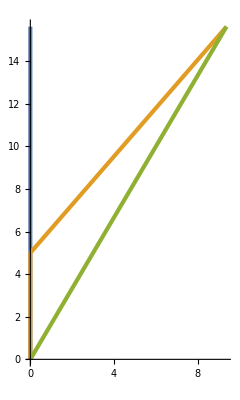

```mathematica
ListPlot[{Map[Reverse[#[[{1,2}]]]&,{a0,a1,a2}],Map[Reverse[#[[{1,2}]]]&,{b0,b1,b2}],Map[Reverse[#[[{1,2}]]]&,{c0,c1,c2}]},AspectRatio->Automatic,Joined->True,PlotStyle->AbsoluteThickness[3]]
```

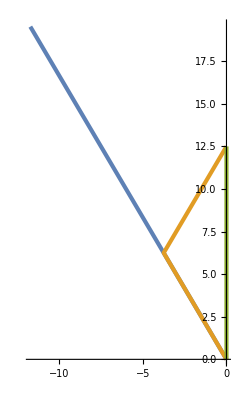

```mathematica
ListPlot[{Map[Reverse[(lor[.6 c].#)[[{1,2}]]]&,{a0,a1,a2}],Map[Reverse[(lor[.6 c].#)[[{1,2}]]]&,{b0,b1,b2}],Map[Reverse[(lor[.6 c].#)[[{1,2}]]]&,{c0,c1,c2}]},AspectRatio->Automatic,Joined->True,PlotStyle->AbsoluteThickness[3]]
```

### Relative Velocities

```mathematica
Va=vel4[{v ,0,0}]
```

{c/(√(1-Abs[v]^2/c^2)),v/(√(1-Abs[v]^2/c^2)),0,0}

```mathematica
Vb=vel4[{vx,vy,vz}]
```

{c/(√(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2)),vx/(√(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2)),vy/(√(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2)),vz/(√(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2))}

```mathematica
La=lor[v]
```

{{1/(√(1-v^2/c^2)),-v/(c √(1-v^2/c^2)),0,0},{-v/(c √(1-v^2/c^2)),1/(√(1-v^2/c^2)),0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
tmp={#,mink[#],vel3[#]}&[La.Vb]
```

{{c/(√(1-v^2/c^2) √(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2))-(v vx)/(c √(1-v^2/c^2) √(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2)),-v/(√(1-v^2/c^2) √(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2))+vx/(√(1-v^2/c^2) √(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2)),vy/(√(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2)),vz/(√(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2))},-vy^2/(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2)-vz^2/(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2)-(-v/(√(1-v^2/c^2) √(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2))+vx/(√(1-v^2/c^2) √(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2)))^2+(c/(√(1-v^2/c^2) √(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2))-(v vx)/(c √(1-v^2/c^2) √(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2)))^2,{(c (-v/(√(1-v^2/c^2) √(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2))+vx/(√(1-v^2/c^2) √(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2))))/(c/(√(1-v^2/c^2) √(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2))-(v vx)/(c √(1-v^2/c^2) √(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2))),(c vy)/(√(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2) (c/(√(1-v^2/c^2) √(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2))-(v vx)/(c √(1-v^2/c^2) √(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2)))),(c vz)/(√(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2) (c/(√(1-v^2/c^2) √(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2))-(v vx)/(c √(1-v^2/c^2) √(1-(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)/c^2))))}}

```mathematica
FullSimplify[tmp[[3]]]
```

{(c^2 (-v+vx))/(c^2-v vx),(c^2 √(1-v^2/c^2) vy)/(c^2-v vx),(c^2 √(1-v^2/c^2) vz)/(c^2-v vx)}

```mathematica
FullSimplify[tmp[[3]]/.v^2->vsq,γ>1]
```

{(c^2 (-v+vx))/(c^2-v vx),(c^2 vy)/(c^2 γ-v vx γ),(c^2 vz)/(c^2 γ-v vx γ)}

### Relativistic rolling

#### Relativistic bike tire

```mathematica
s={t,r Cos[ϕ+ω t],r Sin[ϕ+ω t],0}/.{r->1,t->θ/ω};
```

```mathematica
sp=FullSimplify[lor[-r ω].s/.{c->1,r->1}];
```

```mathematica
FullSimplify[(s/.{θ->2π})-(s/.{θ->0})]
```

{(2 π)/ω,0,0,0}

```mathematica
FullSimplify[(sp/.{θ->2π})-(sp/.{θ->0})]
```

{(2 π)/(ω √(1-ω^2)),(2 π)/(√(1-ω^2)),0,0}

```mathematica
u=Dt[s,τ]/.{Dt[ω,τ]->0,Dt[ϕ,τ]->0,Dt[θ,τ]->γ[ω c] ω};
```

```mathematica
up=FullSimplify[lor[-r ω].u/.{c->1,r->1}];
```

```mathematica
simult=FullSimplify[mink[u,{t,x,y,z}-s]==0,{0<ω<1}]
```

θ+y ω^2 Cos[θ+ϕ]==ω (t+x ω Sin[θ+ϕ])

```mathematica
thetasimul[ωin_,θa_,ϕa_,ϕb_]:=
Module[{simula,worldb},
simula=simult/.{ω->ωin,θ->θa,ϕ->ϕa};
worldb=s/.{ω->ωin,ϕ->ϕb};
simula=simula/.{t->worldb[[1]],x->worldb[[2]],y->worldb[[3]]};
θ/.FindRoot[simula,{θ,θa}]
]
```

```mathematica
thetasimul[.9,0.,0.°,5.°]
```

0.323278

```mathematica
thetasimul[.9,% ,5.°,10.°]
```

0.646556

```mathematica
thetasimul[.9,%,10.°,0.°]
```

0.130748

```mathematica
thetasimul[.9,0.,0.°,10.°]
```

0.515808

```mathematica
Integrate[Evaluate[Simplify[ArcLengthFactor[Rest[s],ϕ]/.{Dt[θ,ϕ]->0,Dt[ω,ϕ]->0}]],{ϕ,-π,π}]
```

2 π

```mathematica
Integrate[Evaluate[Simplify[First[u]ArcLengthFactor[Rest[s],ϕ]/.{Dt[θ,ϕ]->0,Dt[ω,ϕ]->0}]],{ϕ,-π,π}]
```

(2 π)/(√(1-ω^2))

```mathematica
sol=Solve[sp[[1]]==0,ϕ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ→-θ-ArcCos[-θ/ω^2]},{ϕ→-θ+ArcCos[-θ/ω^2]}}

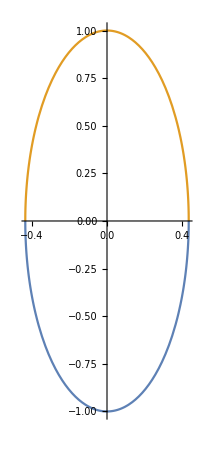

```mathematica
ParametricPlot[Evaluate[sp[[{2,3}]]/.sol/.ω->.9],{θ,-(.9)^2,(.9)^2},AspectRatio->Automatic]
```

```mathematica
int=Integrate[Evaluate[2 FullSimplify[ArcLengthFactor[Rest[sp]/.sol[[1]],θ]/.{Dt[ω,θ]->0},{0<ω<1}]],{θ,-ω^2,ω^2},Assumptions->{0<ω<1}]
```

4 √(1-ω^2) EllipticE[ω^2/(-1+ω^2)]

```mathematica
int/.ω->.9
```

4.68679

```mathematica
With[{a=1,b=1/γ[.9c]},With[{h=(a-b)^2/(a+b)^2},π (a+b)(1+3h/(10+√(4-3h)))]]
```

4.68679

```mathematica
int=Integrate[Evaluate[ FullSimplify[First[up/.sol[[1]]]ArcLengthFactor[Rest[sp]/.sol[[1]],θ]/.{Dt[ω,θ]->0},{0<ω<1}]+FullSimplify[First[up/.sol[[2]]]ArcLengthFactor[Rest[sp]/.sol[[2]],θ]/.{Dt[ω,θ]->0},{0<ω<1}]],{θ,-ω^2,ω^2},Assumptions->{0<ω<1}]
```

(4 EllipticE[ω^2/(-1+ω^2)])/(√(1-ω^2))

```mathematica
int/.ω->.9
```

24.6673

```mathematica
2π γ[.9 c]
```

14.4146

#### Relativistic bike tire2

```mathematica
s={c t,r Cos[ϕ+ω t],r Sin[ϕ+ω t],0}/.{c->1,r->1}
```

{t,Cos[ϕ+t ω],Sin[ϕ+t ω],0}

```mathematica
u=Dt[s,τ,Constants->{c,r,ω,ϕ}]/.{Dt[t,τ,Constants->{c,r,ϕ,ω}]->γ[ω r]}/.{c->1,r->1}
```

{1/(√(1-ω^2)),-(ω Sin[ϕ+t ω])/(√(1-ω^2)),(ω Cos[ϕ+t ω])/(√(1-ω^2)),0}

```mathematica
Simplify[u==(c D[s,t])/(√mink[D[s,t]])/.{c->1,r->1}]
```

True

```mathematica
a=Dt[u,τ,Constants->{c,r,ω,ϕ}]/.{Dt[t,τ,Constants->{c,r,ϕ,ω}]->γ[ω r]}/.{c->1,r->1}
```

{0,-(ω^2 Cos[ϕ+t ω])/(1-ω^2),-(ω^2 Sin[ϕ+t ω])/(1-ω^2),0}

```mathematica
Simplify[a==(c D[u,t])/(√mink[D[s,t]])/.{c->1,r->1}]
```

True

```mathematica
FullSimplify[mink[u]]
```

1

```mathematica
mink[u,a]
```

0

```mathematica
sp=FullSimplify[lor[-r ω].s/.{c->1,r->1}]
```

{(t+ω Cos[ϕ+t ω])/(√(1-ω^2)),(t ω+Cos[ϕ+t ω])/(√(1-ω^2)),Sin[ϕ+t ω],0}

```mathematica
Simplify[(c D[sp,t])/(√mink[D[sp,t]])/.{c->1,r->1}]
```

{(-1+ω^2 Sin[ϕ+t ω])/(-1+ω^2),(ω (-1+Sin[ϕ+t ω]))/(-1+ω^2),(ω Cos[ϕ+t ω])/(√(1-ω^2)),0}

```mathematica
up=FullSimplify[Dt[sp,τ,Constants->{c,r,ω,ϕ}]/.{Dt[t,τ,Constants->{c,r,ϕ,ω}]->γ[ω r]}/.{c->1,r->1}]
```

{(-1+ω^2 Sin[ϕ+t ω])/(-1+ω^2),(ω (-1+Sin[ϕ+t ω]))/(-1+ω^2),(ω Cos[ϕ+t ω])/(√(1-ω^2)),0}

```mathematica
FullSimplify[up==lor[-r ω].u/.{c->1,r->1}]
```

True

```mathematica
ap=FullSimplify[Dt[up,τ,Constants->{c,r,ω,ϕ}]/.{Dt[t,τ,Constants->{c,r,ϕ,ω}]->γ[ω r]}/.{c->1,r->1}]
```

{-(ω^3 Cos[ϕ+t ω])/((1-ω^2)^(3/2)),-(ω^2 Cos[ϕ+t ω])/((1-ω^2)^(3/2)),(ω^2 Sin[ϕ+t ω])/(-1+ω^2),0}

```mathematica
FullSimplify[ap==lor[-r ω].a/.{c->1,r->1}]
```

True

```mathematica
sol=Solve[sp[[1]]==tp,ϕ]
```

{{ϕ→ConditionalExpression[-t ω-ArcCos[(-t+tp √(1-ω^2))/ω]+2 π C[1],C[1]∈Integers]},{ϕ→ConditionalExpression[-t ω+ArcCos[(-t+tp √(1-ω^2))/ω]+2 π C[1],C[1]∈Integers]}}

```mathematica
spsol=FullSimplify[sp/.sol]
```

{{ConditionalExpression[tp,C[1]∈Integers],ConditionalExpression[(tp-t √(1-ω^2))/ω,C[1]∈Integers],ConditionalExpression[-Sin[ArcCos[(-t+tp √(1-ω^2))/ω]-2 π C[1]],C[1]∈Integers],0},{ConditionalExpression[tp,C[1]∈Integers],ConditionalExpression[(tp-t √(1-ω^2))/ω,C[1]∈Integers],ConditionalExpression[Cos[ArcSin[(t-tp √(1-ω^2))/ω]+2 π C[1]],C[1]∈Integers],0}}

```mathematica
trange=t/.Solve[((t-tp √(1-ω^2))^2)/ω^2== 1,t]
```

{-ω+tp √(1-ω^2),ω+tp √(1-ω^2)}

```mathematica
tmp={ω->.9,tp->0};ParametricPlot[spsol[[All,{2,3}]]/.tmp,Evaluate[Prepend[trange/.tmp,t]],PlotStyle->AbsoluteThickness[4],ColorFunction->Function[{x,y,t},Evaluate[If[y>0,Hue[.18+ϕ/(30. °)/.sol[[2]]/.tmp],Hue[.18+ϕ/(30. °)/.sol[[1]]/.tmp]]]],ColorFunctionScaling->False,PlotPoints->360]
```

-Graphics-

```mathematica
tmp={ω->.9,tp->1};ParametricPlot[spsol[[All,{2,3}]]/.tmp,Evaluate[Prepend[trange/.tmp,t]],PlotStyle->AbsoluteThickness[4],ColorFunction->Function[{x,y,t},Evaluate[If[y>0,Hue[.18+ϕ/(30. °)/.sol[[2]]/.tmp],Hue[.18+ϕ/(30. °)/.sol[[1]]/.tmp]]]],ColorFunctionScaling->False,PlotPoints->360]
```

-Graphics-

#### Relativistic barbell

```mathematica
s={c t,r Cos[ω t],r Sin[ω t],0}
```

{c t,r Cos[t ω],r Sin[t ω],0}

```mathematica
u=Dt[s,τ,Constants->{c,r,ω}]/.{Dt[t,τ,Constants->{c,r,ω}]->γ[r ω]}
```

{c/(√(1-(r^2 ω^2)/c^2)),-(r ω Sin[t ω])/(√(1-(r^2 ω^2)/c^2)),(r ω Cos[t ω])/(√(1-(r^2 ω^2)/c^2)),0}

```mathematica
p=m u
```

{(c m)/(√(1-(r^2 ω^2)/c^2)),-(m r ω Sin[t ω])/(√(1-(r^2 ω^2)/c^2)),(m r ω Cos[t ω])/(√(1-(r^2 ω^2)/c^2)),0}

```mathematica
f=Dt[p,τ,Constants->{c,r,ω,m}]/.{Dt[t,τ,Constants->{c,r,ω,m}]->γ[r ω]}
```

{0,-(m r ω^2 Cos[t ω])/(1-(r^2 ω^2)/c^2),-(m r ω^2 Sin[t ω])/(1-(r^2 ω^2)/c^2),0}

```mathematica
Integrate[u ρ[r],{r,-R,R}]
```

{∫_-R^R (c ρ[r])/(√(1-(r^2 ω^2)/c^2))ⅆr,∫_-R^R -(r ω Sin[t ω] ρ[r])/(√(1-(r^2 ω^2)/c^2))ⅆr,∫_-R^R (r ω Cos[t ω] ρ[r])/(√(1-(r^2 ω^2)/c^2))ⅆr,0}

#### Relativistic rotation

Expression for any particle on a wheel centered on the origin and rotating in the counter - clockwise direction with angular frequency ω.  R >= r >= 0 and - π < ϕ <= π.

```mathematica
s={c t,r Cos[ϕ+ω t],r Sin[ϕ+ω t],0}
```

{c t,r Cos[ϕ+t ω],r Sin[ϕ+t ω],0}

```mathematica
u=Dt[s,τ,Constants->{c,r,ϕ,ω}]/.{Dt[t,τ,Constants->{c,r,ϕ,ω}]->γ[ω r]}
```

{c/(√(1-(r^2 ω^2)/c^2)),-(r ω Sin[ϕ+t ω])/(√(1-(r^2 ω^2)/c^2)),(r ω Cos[ϕ+t ω])/(√(1-(r^2 ω^2)/c^2)),0}

```mathematica
FullSimplify[u==(c D[s,t])/(√mink[D[s,t]]),{c>0,r>0,c^2>r^2 ω^2}]
```

True

```mathematica
Simplify[mink[u]]
```

c^2

```mathematica
a=Dt[u,τ,Constants->{c,r,ϕ,ω}]/.{Dt[t,τ,Constants->{c,r,ϕ,ω}]->γ[ω r]}
```

{0,-(r ω^2 Cos[ϕ+t ω])/(1-(r^2 ω^2)/c^2),-(r ω^2 Sin[ϕ+t ω])/(1-(r^2 ω^2)/c^2),0}

```mathematica
FullSimplify[a==(c  D[u,t])/(√mink[D[s,t]]),{c>0,r>0,c^2>r^2 ω^2}]
```

True

```mathematica
FullSimplify[mink[a],{c>0,r>0,c^2>r^2 ω^2}]
```

-(c^4 r^2 ω^4)/((c^2-r^2 ω^2)^2)

```mathematica
γ[r ω]^4
```

1/((1-(r^2 ω^2)/c^2)^2)

```mathematica
FullSimplify[mink[a]==-γ[r ω]^4 r^2 ω^4,{c>0,r>0,c^2>r^2 ω^2}]
```

True

```mathematica
mink[u,a]
```

0

```mathematica
sp=lor[R ω].s
```

{(c t)/(√(1-(R^2 ω^2)/c^2))-(r R ω Cos[ϕ+t ω])/(c √(1-(R^2 ω^2)/c^2)),-(R t ω)/(√(1-(R^2 ω^2)/c^2))+(r Cos[ϕ+t ω])/(√(1-(R^2 ω^2)/c^2)),r Sin[ϕ+t ω],0}

```mathematica
up=FullSimplify[(c D[sp,t])/(√mink[D[sp,t]]),{c>0,R>r>0,c^2>R^2 ω^2>r^2 ω^2>0}]
```

{(c^3+c r R ω^2 Sin[ϕ+t ω])/(√((c-r ω) (c+r ω) (c-R ω) (c+R ω))),-(c ω (R+r Sin[ϕ+t ω]))/(√((c-r ω) (c+r ω) (1-(R^2 ω^2)/c^2))),(c r ω Cos[ϕ+t ω])/(√((c-r ω) (c+r ω))),0}

```mathematica
FullSimplify[mink[up],{c>0,R>r>0,c^2>R^2 ω^2>r^2 ω^2>0}]
```

c^2

```mathematica
FullSimplify[up==lor[R ω].u,{c>0,R>r>0,c^2>R^2 ω^2>r^2 ω^2>0}]
```

True

```mathematica
ap=FullSimplify[(c D[up,t])/(√mink[D[sp,t]]),{c>0,R>r>0,c^2>R^2 ω^2>r^2 ω^2>0}]
```

{(c^2 r R ω^3 Cos[ϕ+t ω])/((c^2-r^2 ω^2) √(c^2-R^2 ω^2)),-(c^3 r ω^2 Cos[ϕ+t ω])/((c^2-r^2 ω^2) √(c^2-R^2 ω^2)),-(c^2 r ω^2 Sin[ϕ+t ω])/(c^2-r^2 ω^2),0}

```mathematica
FullSimplify[mink[ap]/.R->r,{c>0,R>r>0,c^2>R^2 ω^2>r^2 ω^2>0}]
```

-(c^4 r^2 ω^4)/((c^2-r^2 ω^2)^2)

```mathematica
FullSimplify[mink[ap,up],{c>0,R>r>0,c^2>R^2 ω^2>r^2 ω^2>0}]
```

0

```mathematica
FullSimplify[ap==lor[R ω].a,{c>0,R>r>0,c^2>R^2 ω^2>r^2 ω^2>0}]
```

True

#### Relativistic rotation in cylindrical rotating frame

The metric in a rotating frame in cylindrical coordinates is given by
ds^2==-(1-(r^2 ω^2)/c^2)c^2 dt^2+dr^2+2 r^2 ω dt dθ+r^2 dθ^2+dz^2
or if parameterized by λ
(ds/dλ)^2==-(1-(r^2 ω^2)/c^2)c^2(dt/dλ)^2+(dr/dλ)^2+2 r^2 ω dt/dλ dθ/dλ+r^2(dθ/dλ)^2+(dz/dλ)^2
also make the substitution
G=γ[r ω]=1/(√(1-(r^2 ω^2)/c^2))

```mathematica
MatrixForm[g={{-G^-2 c^2,0,r^2 ω,0},{0,1,0,0},{r^2 ω,0,r^2,0},{0,0,0,1}}]
```

(-c^2/G^2 | 0 | r^2 ω | 0
0 | 1 | 0 | 0
r^2 ω | 0 | r^2 | 0
0 | 0 | 0 | 1)

The worldline in this coordinate system for a particle undergoing uniform circular motion with angular velocity ω at radius r=r0, θ=0, and z=0 is given by

```mathematica
s={t,r0,0,0}
```

{t,r0,0,0}

```mathematica
u=Simplify[I c D[s,t]/(√(g.D[s,t].D[s,t])),{0<c,1<G}]
```

{G,0,0,0}

```mathematica
u.u
```

G^2

```mathematica
(g.u).u
```

-c^2

```mathematica
a=I c D[u,t]/(√(g.D[s,t].D[s,t]))+{0,-ω^2 r,0,0}(u.u)
```

{0,-G^2 r ω^2,0,0}

```mathematica
g.a.a
```

G^4 r^2 ω^4

```mathematica
Simplify[g.a.a==γ[r ω]^4 r^2 ω^4,{0<r ω<c}]
```

r^2 ω^4 (G^4-1/((-1+(r^2 ω^2)/c^2)^2))==0

#### Relativistic rotation in cylindrical rotating frame (gamma expanded)

The metric in a rotating frame in cylindrical coordinates is given by
ds^2==-(1-(r^2 ω^2)/c^2)c^2 dt^2+dr^2+2 r^2 ω dt dθ+r^2 dθ^2+dz^2
or if parameterized by λ
(ds/dλ)^2==-(1-(r^2 ω^2)/c^2)c^2(dt/dλ)^2+(dr/dλ)^2+2 r^2 ω dt/dλ dθ/dλ+r^2(dθ/dλ)^2+(dz/dλ)^2

```mathematica
x={t,r,θ,z}
```

{t,r,θ,z}

```mathematica
MatrixForm[g={{-(1-(r^2 ω^2)/c^2)c^2,0,r^2 ω,0},{0,1,0,0},{r^2 ω,0,r^2,0},{0,0,0,1}}]
```

(c^2 (-1+(r^2 ω^2)/c^2) | 0 | r^2 ω | 0
0 | 1 | 0 | 0
r^2 ω | 0 | r^2 | 0
0 | 0 | 0 | 1)

```mathematica
MatrixForm[Γ=FullSimplify[Table[Sum[1/2((Inverse[g])[[i,m]])(D[g[[m,k]],x[[l]]]+D[g[[m,l]],x[[k]]]-D[g[[k,l]],x[[m]]]),{m,4}],{i,4},{k,4},{l,4}],{0<R<r}],TableDepth->2]
```

({0,0,0,0} | {0,0,0,0} | {0,0,0,0} | {0,0,0,0}
{-r ω^2,0,-r ω,0} | {0,0,0,0} | {-r ω,0,-r,0} | {0,0,0,0}
{0,ω/r,0,0} | {ω/r,0,1/r,0} | {0,1/r,0,0} | {0,0,0,0}
{0,0,0,0} | {0,0,0,0} | {0,0,0,0} | {0,0,0,0})

The worldline in this coordinate system for a particle undergoing uniform circular motion with angular velocity ω at radius r=r0, θ=0, and z=0 is given by

```mathematica
x={t,r0,0,0}
```

{t,r0,0,0}

```mathematica
u=I c D[x,t]/(√(g.D[x,t].D[x,t]))
```

{(ⅈ c)/(√(c^2 (-1+(r^2 ω^2)/c^2))),0,0,0}

```mathematica
Simplify[u,{0<c,1<G}]
```

{(ⅈ c)/(√(-c^2+r^2 ω^2)),0,0,0}

```mathematica
(g.u).u
```

-c^2

```mathematica
a=Table[I c(D[u,t]/(√(g.D[x,t].D[x,t])))[[λ]]+Sum[(Γ[[λ,μ,ν]])u[[μ]]u[[ν]],{μ,4},{ν,4}],{λ,4}]
```

{0,(r ω^2)/(-1+(r^2 ω^2)/c^2),0,0}

```mathematica
g.a.u
```

0

```mathematica
g.a.a
```

(r^2 ω^4)/((-1+(r^2 ω^2)/c^2)^2)

```mathematica
Simplify[g.a.a==γ[r ω]^4 r^2 ω^4,{0<r ω<c}]
```

True

Now find the coordinate acceleration for a geodesic

```mathematica
x={t,r[t],θ[t],z[t]}
```

{t,r[t],θ[t],z[t]}

```mathematica
u=Simplify[I c D[x,t]/(√((g/.{r->r[t],θ->θ[t],z->z[t]}).D[x,t].D[x,t]))]
```

{(ⅈ c)/(√(-c^2+r'[t]^2+z'[t]^2+r[t]^2 (ω+θ'[t])^2)),(ⅈ c r'[t])/(√(-c^2+r'[t]^2+z'[t]^2+r[t]^2 (ω+θ'[t])^2)),(ⅈ c θ'[t])/(√(-c^2+r'[t]^2+z'[t]^2+r[t]^2 (ω+θ'[t])^2)),(ⅈ c z'[t])/(√(-c^2+r'[t]^2+z'[t]^2+r[t]^2 (ω+θ'[t])^2))}

```mathematica
Simplify[(g/.{r->r[t],θ->θ[t],z->z[t]}).u.u]
```

-c^2

```mathematica
a=Simplify[Table[I c(D[u,t]/(√((g/.{r->r[t],θ->θ[t],z->z[t]}).D[x,t].D[x,t])))[[λ]]+Sum[(Γ[[λ,μ,ν]]/.{r->r[t],θ->θ[t],z->z[t]})u[[μ]]u[[ν]],{μ,4},{ν,4}],{λ,4}]]
```

{(c^2 (r[t] r'[t] (ω+θ'[t])^2+r'[t] r''[t]+z'[t] z''[t]+r[t]^2 (ω+θ'[t]) θ''[t]))/((-c^2+r'[t]^2+z'[t]^2+r[t]^2 (ω+θ'[t])^2)^2),(c^2 (-r[t] (c^2-2 r'[t]^2-z'[t]^2) (ω+θ'[t])^2+r[t]^3 (ω+θ'[t])^4+(c^2-z'[t]^2) r''[t]+r'[t] z'[t] z''[t]-r[t]^2 (ω+θ'[t]) ((ω+θ'[t]) r''[t]-r'[t] θ''[t])))/(-c^2+r'[t]^2+z'[t]^2+r[t]^2 (ω+θ'[t])^2)^2,(c^2 (-2 r'[t]^3 (ω+θ'[t])+r'[t] (2 (c^2-z'[t]^2) (ω+θ'[t])-r[t]^2 (ω+θ'[t])^2 (2 ω+θ'[t])+r[t] θ'[t] r''[t])-r[t] r'[t]^2 θ''[t]-r[t] (-z'[t] θ'[t] z''[t]+z'[t]^2 θ''[t]+(-c^2+ω r[t]^2 (ω+θ'[t])) θ''[t])))/(r[t] (-c^2+r'[t]^2+z'[t]^2+r[t]^2 (ω+θ'[t])^2)^2),(c^2 (r[t] r'[t] z'[t] (ω+θ'[t])^2+r'[t] z'[t] r''[t]+c^2 z''[t]-r'[t]^2 z''[t]-r[t]^2 (ω+θ'[t]) ((ω+θ'[t]) z''[t]-z'[t] θ''[t])))/(-c^2+r'[t]^2+z'[t]^2+r[t]^2 (ω+θ'[t])^2)^2}

```mathematica
Simplify[(g/.{r->r[t],θ->θ[t],z->z[t]}).a.u]
```

0

```mathematica
Simplify[Solve[{0==a[[2]],0==a[[3]],0==a[[4]]},{r''[t],θ''[t],z''[t]}]]
```

{{r''[t]→r[t] (ω+θ'[t])^2,θ''[t]→-(2 r'[t] (ω+θ'[t]))/r[t],z''[t]→0}}

```mathematica
Simplify[a/.{r->Function[t,√((t vx+x0)^2+(t vy+y0)^2)],θ->Function[t,ArcTan[t vx+x0,t vy+y0]-ω t],z->Function[t,t vz+z0]}]
```

{0,0,0,0}

### Generalized de Broglie formula p == {m γ c, m γ v} == {e/c, p} == h {f/c, 1/λ} == h k

```mathematica
lor[-0.0 c].{ElectronMass SpeedOfLight,0,0,0}
```

{0.+(2.73092×10^-22 Kilogram Meter)/Second,0.,0.,0.}

```mathematica
Map[Convert[#,1/Meter]&,%/PlanckConstant]
```

{(4.12148×10^11)/Meter,0.,0.,0.}

```mathematica
%[[1]] SpeedOfLight
```

(1.23559×10^20)/Second

```mathematica
lor[-0.6 c].{ElectronMass SpeedOfLight,0,0,0}
```

{0.+(3.41366×10^-22 Kilogram Meter)/Second,0.+(2.04819×10^-22 Kilogram Meter)/Second,0.,0.}

```mathematica
Map[Convert[#,1/Meter]&,%/PlanckConstant]
```

{(5.15186×10^11)/Meter,(3.09111×10^11)/Meter,0.,0.}

```mathematica
%[[1]] SpeedOfLight
```

(1.54449×10^20)/Second

```mathematica
Out[52]/Out[49]
```

{{4.68679/(ϕ→-θ-ArcCos[-θ/ω^2])},{4.68679/(ϕ→-θ+ArcCos[-θ/ω^2])}}

```mathematica
Solve[{e /c,p,0,0}==h{f/c,1/λ,0,0},{e,p}][[1]]
```

Solve::ivar: {c\ m/√1 - r^2\ ω^2/c^2, -m\ r\ ω\ Sin[t\ ω]/√1 - r^2\ ω^2/c^2, m\ r\ ω\ Cos[t\ ω]/√1 - r^2\ ω^2/c^2, 0} is not a valid variable.

{e/c,{(c m)/(√(1-(r^2 ω^2)/c^2)),-(m r ω Sin[t ω])/(√(1-(r^2 ω^2)/c^2)),(m r ω Cos[t ω])/(√(1-(r^2 ω^2)/c^2)),0},0,0}=={{0,-(h m r ω^2 Cos[t ω])/(c (1-(r^2 ω^2)/c^2)),-(h m r ω^2 Sin[t ω])/(c (1-(r^2 ω^2)/c^2)),0},h/λ,0,0}

```mathematica
Solve[{e /c,p,0,0}==h{f/c,1/λ,0,0},{f,λ}][[1]]
```

Solve::ivar: {0, -m\ r\ ω^2\ Cos[t\ ω]/1 - r^2\ ω^2/c^2, -m\ r\ ω^2\ Sin[t\ ω]/1 - r^2\ ω^2/c^2, 0} is not a valid variable.

{e/c,{(c m)/(√(1-(r^2 ω^2)/c^2)),-(m r ω Sin[t ω])/(√(1-(r^2 ω^2)/c^2)),(m r ω Cos[t ω])/(√(1-(r^2 ω^2)/c^2)),0},0,0}=={{0,-(h m r ω^2 Cos[t ω])/(c (1-(r^2 ω^2)/c^2)),-(h m r ω^2 Sin[t ω])/(c (1-(r^2 ω^2)/c^2)),0},h/λ,0,0}

#### In moving frame

```mathematica
k={m γ c,m γ v,0,0}/h
```

{(c m γ)/h,(m v γ)/h,0,0}

```mathematica
1/k[[2]]
```

h/(m v γ)

```mathematica
k0=k/.{γ->γ[v]}/.{v->.5c}/.{c->1,m->1,h->1}
```

{1.1547,0.57735,0,0}

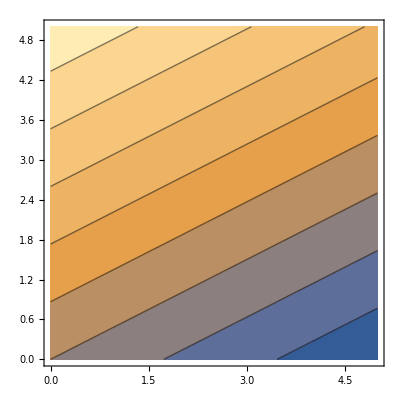

```mathematica
ContourPlot[mink[{t,x,0,0},k0],{x,0,5},{t,0,5},PlotPoints->101,Contours->Range[-5,6]]
```

#### Transform from moving frame to rest frame

```mathematica
k=lorentz.k
```

{(c m γ^2)/h-(m v^2 γ^2)/(c h),0,0,0}

```mathematica
Simplify[k/.γ->gamma]
```

{(c m)/h,0,0,0}

```mathematica
1/k[[2]]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

#### In rest frame

```mathematica
k={m γ c,m γ v,0,0}/h/.{γ->γ[v]}/.{v->0}
```

{(c m)/h,0,0,0}

```mathematica
1/k[[2]]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

#### Transform from rest frame to moving frame

```mathematica
k=lorentz.k
```

{(c m γ)/h,-(m v γ)/h,0,0}

```mathematica
1/k[[2]]
```

-h/(m v γ)

### Doppler stuff

```mathematica
c=1;
```

```mathematica
ab=lor[-.5];
vb=ab.(vbp=vel4[{0,0,0}]);
vc=ab.(vcp=vel4[{0,0,0}]);
vr=ab.(vrp=vel4[{.3,0,0}]);
vu=ab.(vup=vel4[{0,-.3,0}]);
vl=ab.(vlp=vel4[{-.3,0,0}]);
vd=ab.(vdp=vel4[{0,.3,0}]);
```

```mathematica
va=vel4[{0,0,0}];
p={e,-e,0,0};
```

```mathematica
{mink[vb,p]/mink[vc,p],mink[vb,p]/mink[vr,p],mink[vb,p]/mink[vu,p],mink[vb,p]/mink[vl,p],mink[vb,p]/mink[vd,p]}
```

{1,(0.+1.73205 e)/(0.+2.36039 e),(0.+1.73205 e)/(0.+1.81568 e),(0.+1.73205 e)/(0.+1.27098 e),(0.+1.73205 e)/(0.+1.81568 e)}

```mathematica
{mink[va,p]/mink[vc,p],mink[va,p]/mink[vr,p],mink[va,p]/mink[vu,p],mink[va,p]/mink[vl,p],mink[va,p]/mink[vd,p]}
```

{e/(0.+1.73205 e),e/(0.+2.36039 e),e/(0.+1.81568 e),e/(0.+1.27098 e),e/(0.+1.81568 e)}